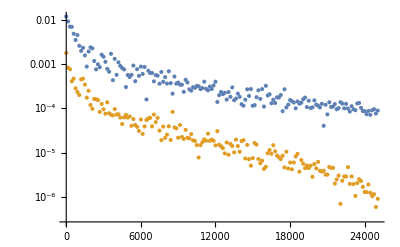
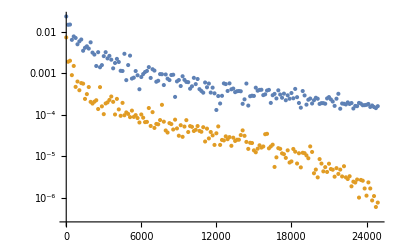
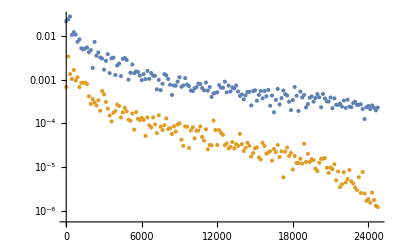
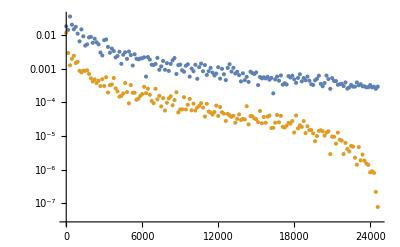
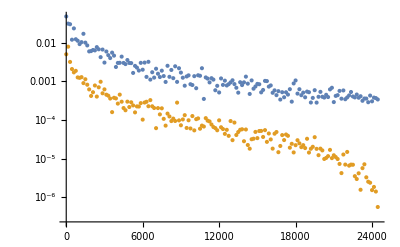
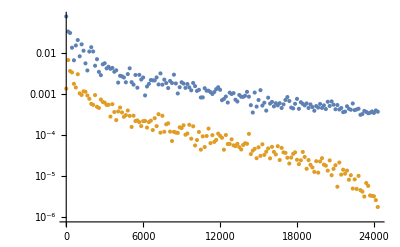
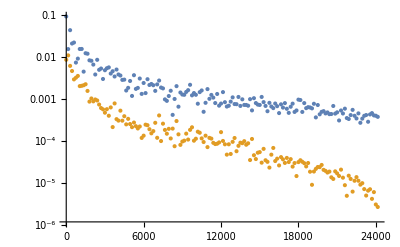
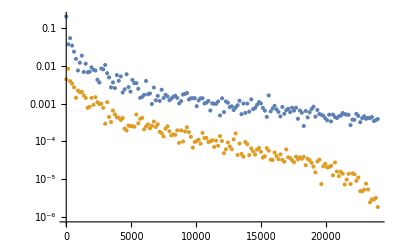

```mathematica
(* CHARTWALLS CORRECTION *) 

(* BROKEN due to bug: *) 
(* these charts show mean squared error over for different window sizes*) 
(data = getRfFprMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *) #, (* bin width *)150];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])&/@ Range[1,30](* should be 1 & 29! *)
```

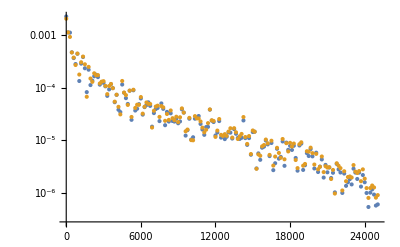
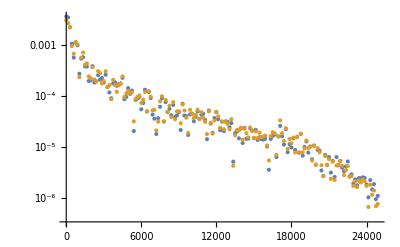
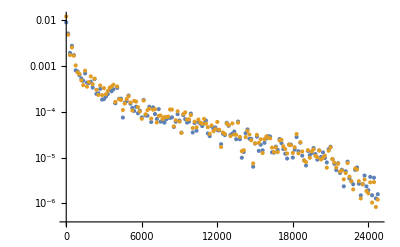
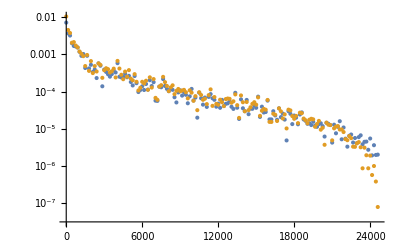
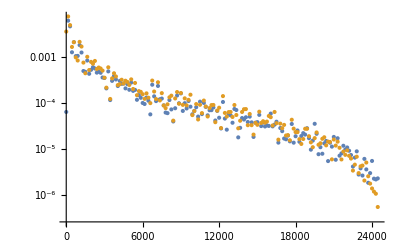
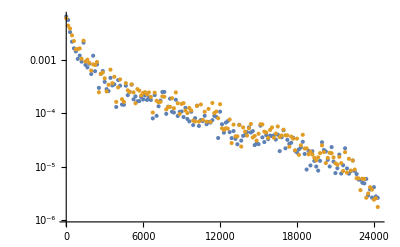
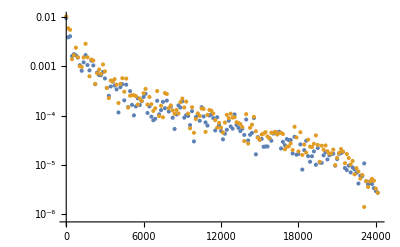
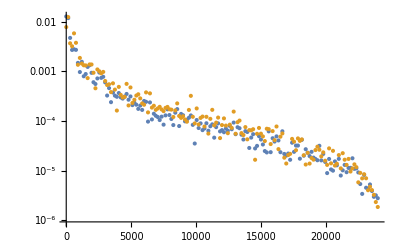

```mathematica
(* FIXED BUG: *) 
(data = getRfFprMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *) #, (* bin width *)150];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])&/@ Range[1,29](* should be 1 & 29! *)
```

```mathematica
data
```

{{0,5,0.00169399,0.00147581},{150,22,0.000917331,0.00178213},{300,21,0.000423161,0.00143357},{450,18,0.000256778,0.00091279},{600,21,0.000229425,0.000644467},{750,17,0.000415323,0.000829207},{900,26,0.000230837,0.000439529},{1050,17,0.00010057,0.000827351},{1200,23,0.000118634,0.000401003},{1350,24,0.000163933,0.000528358},{1500,15,0.0000790642,0.00036913},{1650,24,0.0000611417,0.000230628},{1800,25,0.000126009,0.000368142},{1950,13,0.000113017,0.000213257},{2100,20,0.000123135,0.000163302},{2250,23,0.0000542954,0.000270017},{2400,20,0.0000675583,0.000335258},{2550,18,0.000059767,0.000131632},{2700,24,0.0000526116,0.0002568},{2850,29,0.0000858581,0.000217617},{3000,18,0.0000330121,0.000141502},{3150,23,0.0000470352,0.000199418},{3300,24,0.0000737942,0.000185945},{3450,18,0.0000653289,0.000280934},{3600,17,0.0000430644,0.000257638},{3750,17,0.0000855155,0.000351264},{3900,23,0.0000360033,0.000114443},{4050,20,0.0000349103,0.0000727296},{4200,15,0.0000271824,0.0000372357},{4350,25,0.0000497764,0.000151963},{4500,17,0.0000444758,0.000143957},{4650,23,0.0000281427,0.000130966},{4800,22,0.0000337636,0.0000558721},{4950,9,0.0000723704,0.000112013},{5100,24,0.0000367084,0.0000958859},{5250,17,0.000042284,0.000126265},{5400,20,0.0000293865,0.0000849498},{5550,24,0.0000172679,0.000108162},{5700,23,0.0000255882,0.0000699419},{5850,16,0.0000276356,0.000063712},{6000,25,0.0000236553,0.000131086},{6150,16,0.0000112608,0.000062945},{6300,18,0.0000169306,0.0000779595},{6450,23,0.0000154768,0.0000713072},{6600,27,0.000017848,0.0000521245},{6750,22,0.0000259687,0.0000536438},{6900,26,0.0000179094,0.000058797},{7050,20,0.0000128835,0.0000433547},{7200,17,0.0000260066,0.0000544178},{7350,24,0.0000144466,0.0000520726},{7500,16,0.0000297948,0.0000552017},{7650,23,0.0000277823,0.000137206},{7800,29,0.0000118233,0.0000595174},{7950,20,0.0000183206,0.000053344},{8100,20,0.0000120221,0.0000464875},{8250,17,0.0000141753,0.0000517354},{8400,21,0.0000114323,0.0000357767},{8550,17,0.0000147422,0.0000433412},{8700,31,0.0000146337,0.0000282477},{8850,23,0.0000119084,0.0000412588},{9000,17,6.22563×10^-6,0.0000357174},{9150,18,0.0000192975,0.000047653},{9300,17,0.0000122474,0.0000545945},{9450,20,0.0000118984,0.0000461699},{9600,23,0.000015818,0.0000500507},{9750,18,0.0000114554,0.0000456853},{9900,17,9.7735×10^-6,0.0000495424},{10050,22,0.0000165732,0.0000416907},{10200,33,0.0000167598,0.0000566138},{10350,19,8.5539×10^-6,0.000040501},{10500,20,8.70529×10^-6,0.0000293243},{10650,18,4.30149×10^-6,0.0000285885},{10800,24,0.0000104855,0.0000368588},{10950,20,5.14033×10^-6,0.0000398397},{11100,17,6.29134×10^-6,0.0000297877},{11250,21,7.51459×10^-6,0.0000235419},{11400,17,4.69175×10^-6,0.0000268661},{11550,21,4.60828×10^-6,0.0000403856},{11700,15,4.07306×10^-6,0.0000141183},{11850,28,9.66649×10^-6,0.0000287236},{12000,24,5.55418×10^-6,0.0000434138},{12150,23,6.46632×10^-6,0.0000373142},{12300,18,0.0000125682,0.0000222142},{12450,20,9.3564×10^-6,0.0000366108},{12600,23,5.24819×10^-6,0.000015814},{12750,29,7.44144×10^-6,0.0000352373},{12900,19,2.50537×10^-6,0.0000255},{13050,14,4.63127×10^-6,0.0000134245},{13200,21,3.60435×10^-6,0.0000188766},{13350,23,5.74792×10^-6,0.0000132302},{13500,10,2.91567×10^-6,0.0000145014},{13650,19,4.97832×10^-6,0.0000124364},{13800,32,4.66142×10^-6,0.0000160113},{13950,12,4.12039×10^-6,0.0000215876},{14100,15,3.90515×10^-6,0.0000256064},{14250,24,3.68272×10^-6,0.0000167301},{14400,23,5.53407×10^-6,0.0000231273},{14550,24,6.10583×10^-6,0.0000237885},{14700,16,6.98601×10^-6,0.0000185802},{14850,19,5.47023×10^-6,0.0000183411},{15000,16,3.36461×10^-6,0.0000216454},{15150,26,2.92297×10^-6,0.0000108174},{15300,20,3.09415×10^-6,0.0000275707},{15450,22,2.46095×10^-6,0.0000147203},{15600,14,4.82982×10^-6,6.92663×10^-6},{15750,17,4.1534×10^-6,0.0000170788},{15900,22,4.89297×10^-6,0.0000161057},{16050,27,2.48055×10^-6,0.0000118968},{16200,18,2.03149×10^-6,0.0000109381},{16350,18,1.78897×10^-6,0.0000235756},{16500,25,2.27067×10^-6,0.0000168871},{16650,20,3.11075×10^-6,0.0000195007},{16800,14,2.66743×10^-6,0.0000246169},{16950,21,1.67595×10^-6,0.0000113709},{17100,14,2.54389×10^-6,0.0000180664},{17250,19,2.25815×10^-6,0.0000170885},{17400,28,1.9121×10^-6,0.0000198029},{17550,21,2.25386×10^-6,4.92075×10^-6},{17700,28,2.21261×10^-6,0.0000115164},{17850,21,1.96055×10^-6,6.65569×10^-6},{18000,25,1.86669×10^-6,7.74485×10^-6},{18150,23,2.4106×10^-6,7.02076×10^-6},{18300,19,1.73493×10^-6,8.26726×10^-6},{18450,20,1.28247×10^-6,6.67182×10^-6},{18600,20,1.69537×10^-6,9.40609×10^-6},{18750,16,1.24571×10^-6,7.7107×10^-6},{18900,21,2.09421×10^-6,2.96774×10^-6},{19050,22,1.3453×10^-6,7.36699×10^-6},{19200,18,4.35526×10^-7,9.70455×10^-6},{19350,23,9.56472×10^-7,0.0000108831},{19500,19,7.70894×10^-7,6.39565×10^-6},{19650,20,1.24841×10^-6,5.57607×10^-6},{19800,18,1.09007×10^-6,7.77359×10^-6},{19950,23,1.05863×10^-6,8.73894×10^-6},{20100,23,5.82658×10^-7,4.79434×10^-6},{20250,20,6.3002×10^-7,7.01567×10^-6},{20400,18,6.12744×10^-7,4.36715×10^-6},{20550,27,8.03465×10^-7,3.18511×10^-6},{20700,19,3.33798×10^-7,4.83892×10^-6},{20850,18,5.38054×10^-7,4.24541×10^-6},{21000,49,3.31141×10^-7,3.61005×10^-6}}

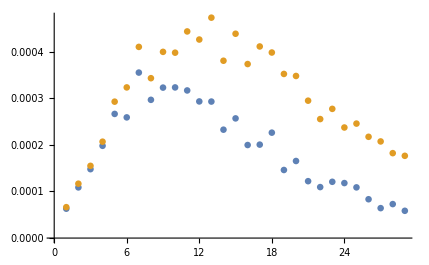
```mathematica
(*** DEPENDENCY OF MSE ON WINDOW ***) 
data = With[{reslist = getRfFNRPointEstResidualsWithH0ct[{4,5,6,7},(*samples per subset size*) 40, (*winsize*)#]}, {{#,Mean@(reslist[[All,2]]^2)},{#,Mean@(reslist[[All,3]]^2)}}]& /@ Range[1,29]; 
ListPlot@Transpose@data
-Graphics-
```

```mathematica
data
```

{{{1,0.000063005},{1,0.00006633}},{{2,0.000108733},{2,0.000116695}},{{3,0.000147854},{3,0.000155008}},{{4,0.000197975},{4,0.000206853}},{{5,0.000266448},{5,0.000292741}},{{6,0.000258999},{6,0.000323335}},{{7,0.000355161},{7,0.000410274}},{{8,0.000296666},{8,0.00034309}},{{9,0.000322902},{9,0.000399628}},{{10,0.000323301},{10,0.000397866}},{{11,0.000316805},{11,0.000443458}},{{12,0.000293237},{12,0.000426063}},{{13,0.000292954},{13,0.000473013}},{{14,0.000232609},{14,0.000380566}},{{15,0.000256844},{15,0.000438488}},{{16,0.000199685},{16,0.000373469}},{{17,0.000200537},{17,0.000411195}},{{18,0.00022623},{18,0.000398195}},{{19,0.000146102},{19,0.000352227}},{{20,0.000165402},{20,0.000347868}},{{21,0.000122094},{21,0.000294853}},{{22,0.000109395},{22,0.000255359}},{{23,0.000120777},{23,0.000277285}},{{24,0.000118029},{24,0.000237283}},{{25,0.000108777},{25,0.000245676}},{{26,0.000083317},{26,0.000217328}},{{27,0.0000642318},{27,0.000207374}},{{28,0.000072918},{28,0.000182238}},{{29,0.0000585122},{29,0.000176517}}}